# Test how well a beta distribution fits the luminosity distribution

### Load data, restrict to packets leaving the supernova

```mathematica
SetDirectory[NotebookDirectory[]];
h5data=Transpose[Import["real_tardis_250.h5", {"Datasets", {"/nus", "/energies"}}],{3,1,2}];
run=10;
data=Cases[h5data[[run]],{ν_,L_} /;L>0];
sortedData=SortBy[data,First];
Dimensions[data]
(* transpose gives list with two sublist, the ν and L, WeightedData expects two separate lists, so use Apply=@@ *)wd=WeightedData@@Transpose[data];
MinMax[wd["InputData"]]
binWidth=(%[[2]]-%[[1]])/1000
Histogram[wd, 2000]
```

{74784,2}

{1.47944×10^13,4.28255×10^15}

4.26775×10^12

-Graphics-

```mathematica
Histogram[sortedData[[50501;;51000,2]]]
```

-Graphics-

### For many samples, there is some discrepancy around 0.96 and at the mode. By eye, the match is better for 100-500 samples. Fine even at the end of the frequency spectrum. Normalize to overall largest luminosity x fudge factor for numerical stability. With max(samples), need more samples to converge to zero at x=1. The method-of-moments estimator is easier to compute (no numerical optimization needed) but for same samples it can diverge at 1 whereas max-likelihood looks fine Check 51700;;52000 to see the difference. Even max-like. doesn’t yield a very good fit.

BetaDistribution[49.8327,1.40569]

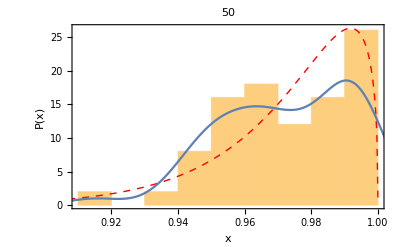

{1.33646,19.5861}

```mathematica
samples=sortedData[[50501;;50550,2]];
(*samples /=Max[samples](1+10^-7);*)
samples /=Max[sortedData[[;;,2]]](1+10^-6);
edist=EstimatedDistribution[samples, BetaDistribution[a,b],
ParameterEstimator->"MaximumLikelihood"]
(*ParameterEstimator->"MethodOfMoments"]*)
Show[Histogram[samples,"Knuth","ProbabilityDensity",Frame->True, FrameLabel-> {"x","P(x)"}, PlotLabel->Length[samples]],
Plot[PDF[edist,x],{x,0,1},PlotStyle->{Red,Thick,Dashed}],
SmoothHistogram[samples,PlotRange->Full]]
Export["beta.pdf", %];
PDF[edist,MinMax[samples]]
```

```mathematica
sortedData[[52000]]
sortedData[[55000]]
```

{1.04217×10^15,1.36694×10^38}

{1.09284×10^15,1.43525×10^38}

```mathematica
NIntegrate[1/Beta[a,b]^2 r^(a-1)s^(b-1),{a,1,∞},{b,1,∞}]
```

NIntegrate::inumr: The integrand (r^(-1+a) s^(-1+b))/Beta[a,b]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,1.},{∞,1.}}.

NIntegrate[(r^(a-1) s^(b-1))/Beta[a,b]^2,{a,1,∞},{b,1,∞}]

```mathematica
Gamma[1/2]
```

√π

```mathematica
Assuming[ Reals&&α>0&&L>0,Integrate[(L2(L-L2))^(α-1)Gamma[α]^-2,{L2,0,∞}]]
```

ConditionalExpression[((-4)^-α L^(-1+2 α) Gamma[1/2-α])/(√π Gamma[α]),α<1/2]

```mathematica
Integrate[Exp[t L]PDF[GammaDistribution[α,1/β],L],{L,0,∞}]
```

Piecewise[{{(1/β)^-α (-t+β)^-α, Re[t]-Re[β]<0&&Re[α]>0}, {Integrate[ⅇ^(L t) (Piecewise[{{(ⅇ^(-L β) L^(-1+α) (1/β)^-α)/Gamma[α], L>0}, {0, True}}]),{L,0,∞},Assumptions→Re[t]-Re[β]≥0||Re[α]≤0], True}}]

```mathematica
Integrate[PDF[GammaDistribution[α,β],L-L2]PDF[GammaDistribution[α,β],L2],{L2,0,∞},Assumptions->α>0&&L>0]
```

(ⅇ^(-L/β) L^(-1+2 α) β^(-2 α))/Gamma[2 α]

```mathematica
(*μ={μ1,μ2};Σ={{Subscript[σ, 11]^2,ρ Subscript[σ, 11] Subscript[σ, 22]},{ρ Subscript[σ, 11] Subscript[σ, 22],Subscript[σ, 22]^2}};Integrate[PDF[MultinormalDistribution[μ,Σ],{α,β}]PDF[GammaDistribution[n α,β],L],{α,0,∞},{β,0,∞}]*)
```

## Test a fit of a Gamma distribution to the samples. Rescale and mirror samples.

{0.0931603,0.0933417}

{α→1.46054,β→58.0912}

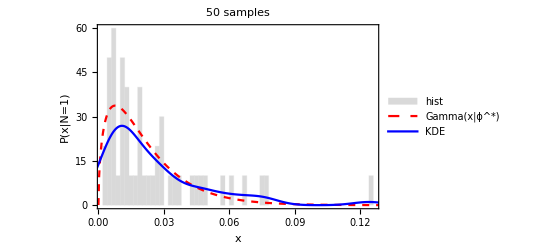

{30.1652,0.0342881}

-Graphics-

```mathematica
nmin=11111;nmax=nmin+49;
{sortedData[[nmin,1]],sortedData[[nmax,1]]}/ Max[sortedData[[All,1]]]
samples=sortedData[[nmin;;nmax,2]];
(*samples /=Max[samples](1+10^-7);*)
samples /=-Max[sortedData[[;;,2]]](1+10^-6);
samples+=1;
gammaDist=GammaDistribution[α,1/β];
pars=FindDistributionParameters[samples, gammaDist,
ParameterEstimator->"MaximumLikelihood"]
gammaDist=gammaDist/.{α->1.5551,β->72.5};
(*gammaDist=gammaDist/.pars;*)
Show[Legended[Histogram[samples,80,"ProbabilityDensity",Frame->True, FrameLabel-> {"x","P(x|N=1)"}, PlotLabel->ToString[Length[samples]]<>" samples",ChartStyle->LightGray],SwatchLegend[{LightGray},{"hist"}]],
Legended[Plot[PDF[gammaDist,x],{x,0,1},PlotStyle->{Red,Thick,Dashed},PlotRange->Full],LineLegend[{Directive[Red,Thick,Dashed]},{"Gamma(x|ϕ^*)"}]],
Legended[SmoothHistogram[samples,PlotRange->Full,PlotStyle->Blue],LineLegend[{Directive[Blue]},{"KDE"}]]
]
Export["gamma.pdf", %];
PDF[gammaDist,MinMax[samples]]
Histogram[sortedData[[nmin;;nmax,2]]]
```

```mathematica
samples[[1000;;1005]]
```

{0.0098313,0.00554383,0.0494208,0.0271855,0.00635476,0.0143337}

```mathematica
Legended[
```

a

## Try different priors for the two Gamma parameters from [Moala et al. 2013]

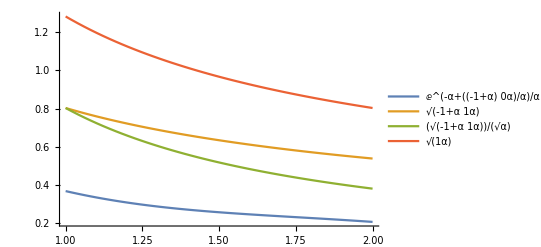

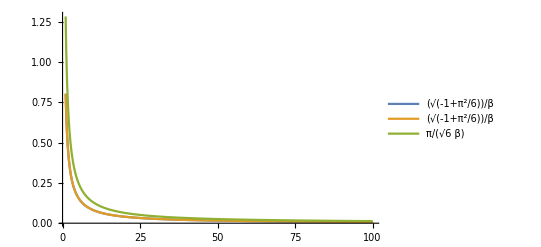

```mathematica
priors[α_,β_,mdip]:=β/Gamma[α] Exp[(α-1)PolyGamma[0,α]/Gamma[α]-α];
priors[α_,β_,jeffreys]:=(√(α PolyGamma[1,α]-1))/β;
priors[α_,β_,ref1]:=priors[α,β,jeffreys]/(√α);priors[α_,β_,ref2]:=(√PolyGamma[1,α])/β;
Plot[Evaluate[priors[α,1,#]&/@{mdip,jeffreys,ref1,ref2}],{α,1,2},PlotLegends->"Expressions"]
Plot[Evaluate[priors[1,β,#]&/@{jeffreys,ref1,ref2}],{β,1,100},PlotLegends->"Expressions"]
```

```mathematica
gradPrior[prior_]:=Grad[Log[prior],{α,β}]
hessPrior[prior_]:=-D[Grad[prior,{α,β}],{{α,β}}]
gradPrior[priors[α,β,jeffreys]]
hessPrior[priors[α,β,jeffreys]]//MatrixForm
```

{(PolyGamma[1,α]+α PolyGamma[2,α])/(2 (-1+α PolyGamma[1,α])),-1/β}

((PolyGamma[1,α]+α PolyGamma[2,α])^2/(4 β (-1+α PolyGamma[1,α])^(3/2))-(2 PolyGamma[2,α]+α PolyGamma[3,α])/(2 β √(-1+α PolyGamma[1,α])) | (PolyGamma[1,α]+α PolyGamma[2,α])/(2 β^2 √(-1+α PolyGamma[1,α]))
(PolyGamma[1,α]+α PolyGamma[2,α])/(2 β^2 √(-1+α PolyGamma[1,α])) | -(2 √(-1+α PolyGamma[1,α]))/β^3)

## Unnormalized posterior

mathematica’s PDF is easy to read but slow if invoked hundreds of times

```mathematica
(*loglike[α_,β_,samples_]:=Total[Map[Log[PDF[GammaDistribution[α,1/β],#]]&,samples]]*)
loglike[α_,β_,samples_]:=Module[{sumL,sumLogL,n},
sumL=Total[samples];
sumLogL=Total[Log[samples]];
n=Length[samples];
n(α Log[β]-Log[Gamma[α]])+(α-1) sumLogL-β sumL 
]
logpost[α_,β_,samples_]:=loglike[α,β,samples]+Log[priors[α,β,jeffreys]]
logmean[α_,β_,samples_,L_,N_]:=logpost[α,β,samples]+N α Log[β]-Log[Gamma[N α]]+(N α-1)Log[L]-β L(*Log[PDF[GammaDistribution[N α,1/β],L]]*)
FindArgMax[{logpost[α,β,samples],α>0&&β>0},{{α,1.2},{β,50}}]
(*ContourPlot[Exp[logpost[α,β,samples]],{α,0.5,2},{β,25,35},PlotLegends->Automatic,Contours->3]*)
```

{1.58983,90.9666}

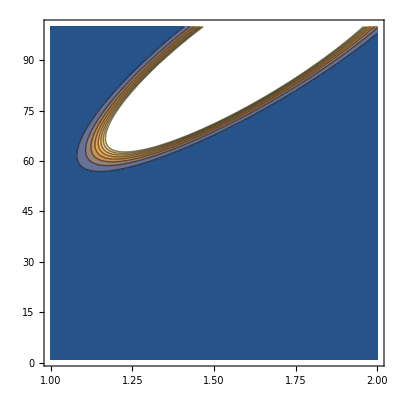

```mathematica
ContourPlot[Exp[logpost[α,β,samples]],{α,1,2},{β,1,100}]
```

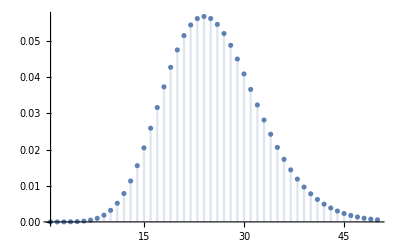

```mathematica
DiscretePlot[PDF[NegativeBinomialDistribution[25+1-1/2,1/2],Nl],{Nl,1,50}]
```

## Laplace approximation of P(L|N,n,l) written as integral over numerator (posterior mean,f) and denominator (evidence, g). Compare with plug-in estimate of α,β.

Hessian of the first and second moment

```mathematica
hess[α_,β_,mom_,pow_]:=Simplify[-D[Grad[Log[Moment[GammaDistribution[α,1/β],mom]^pow],{α,β}],{{α,β}}]]
hess[α_,β_,mom_]:=hess[α,β,mom,1]
hess[α,β,2]
```

ReplaceAll::reps: {solg⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

SetDelayed::write: Tag ReplaceAll in ({{hessLikelihood[α,β,0]+(PolyGamma[«2»]+Times[«2»])^2/(4 β (-1+Times[«2»])^(3/2))-(2 PolyGamma[«2»]+α PolyGamma[«2»])/(2 β √(-1+Times[«2»])),hessLikelihood[α,β,0]+(PolyGamma[1,α]+α PolyGamma[«2»])/(2 β^2 √(-1+Times[«2»]))},{hessLikelihood[α,β,0]+(PolyGamma[1,α]+α PolyGamma[«2»])/(2 β^2 √(-1+Times[«2»])),hessLikelihood[α,β,0]-(2 √(-1+Times[«2»]))/β^3}}/.solg⟦2⟧)[α_,β_,mom_,pow_] is Protected.

$Failed

ReplaceAll::reps: {solg⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

SetDelayed::write: Tag ReplaceAll in ({{hessLikelihood[α,β,0]+(PolyGamma[«2»]+Times[«2»])^2/(4 β (-1+Times[«2»])^(3/2))-(2 PolyGamma[«2»]+α PolyGamma[«2»])/(2 β √(-1+Times[«2»])),hessLikelihood[α,β,0]+(PolyGamma[1,α]+α PolyGamma[«2»])/(2 β^2 √(-1+Times[«2»]))},{hessLikelihood[α,β,0]+(PolyGamma[1,α]+α PolyGamma[«2»])/(2 β^2 √(-1+Times[«2»])),hessLikelihood[α,β,0]-(2 √(-1+Times[«2»]))/β^3}}/.solg⟦2⟧)[α_,β_,mom_] is Protected.

$Failed

ReplaceAll::reps: {solg⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: {{hessLikelihood[α,β,0]+(PolyGamma[«2»]+Times[«2»])^2/(4 β (-1+Times[«2»])^(3/2))-(2 PolyGamma[«2»]+α PolyGamma[«2»])/(2 β √(-1+Times[«2»])),hessLikelihood[α,β,0]+(PolyGamma[1,α]+α PolyGamma[«2»])/(2 β^2 √(-1+Times[«2»]))},{hessLikelihood[α,β,0]+(PolyGamma[1,α]+α PolyGamma[«2»])/(2 β^2 √(-1+Times[«2»])),hessLikelihood[α,β,0]-(2 √(-1+Times[«2»]))/β^3}}/.solg⟦2⟧ called with 3 arguments; 1 argument is expected.

({{hessLikelihood[α,β,0]+(PolyGamma[1,α]+α PolyGamma[2,α])^2/(4 β (-1+α PolyGamma[1,α])^(3/2))-(2 PolyGamma[2,α]+α PolyGamma[3,α])/(2 β √(-1+α PolyGamma[1,α])),hessLikelihood[α,β,0]+(PolyGamma[1,α]+α PolyGamma[2,α])/(2 β^2 √(-1+α PolyGamma[1,α]))},{hessLikelihood[α,β,0]+(PolyGamma[1,α]+α PolyGamma[2,α])/(2 β^2 √(-1+α PolyGamma[1,α])),hessLikelihood[α,β,0]-(2 √(-1+α PolyGamma[1,α]))/β^3}}/.solg⟦2⟧)[α,β,2]

```mathematica
hessLikelihood[α_,β_,n_]:={{n PolyGamma[1,α], -n/β},{-n/β,(n α)/β}}
hessMean[α_,β_,N_]:={{PolyGamma[1,N α],-1/β},{-1/β,(N α)/β}}
(*hessLikelihood[α,β,n]+hessPrior[priors[α,β,jeffreys]]//Simplify
%+hessMean[α,β,Nl]//Simplify
*)detf[α_,β_,n_,N_]:=Det[hessLikelihood[α,β,n]+hessPrior[priors[α,β,jeffreys]]+hessMean[α,β,N]]//Simplify
detg[α_,β_,n_]:=Det[hessLikelihood[α,β,n]+hessPrior[priors[α,β,jeffreys]]]//Simplify
detm[α_,β_,n_,mom_,pow_]:=Det[hessLikelihood[α,β,n]+hessPrior[priors[α,β,jeffreys]]+hess[α,β,mom,pow]]//Simplify
(*detf[α,β,n,Nl]
detg[α,β,n]*)
```

Laplace and plug-in estimate agree very well for N=5. This shows that Laplace is properly normalized. For small N and large n, there is no real difference. For larger N, the posterior predictive is slightly broader. This effect is reduced if more samples are used to learn α and β.
The CLT approx. is even wider than Laplace.

{11621.4,{α→1.39236,β→60.3934}}

405625.

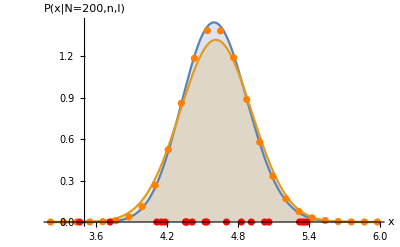

```mathematica
laplace[maxf_,detf_,maxg_,detg_]:=  Exp[maxf-maxg] √(detg/detf)
pL[L_,Nl_,maxg_,detg_]:=Module[{solf},
solf=FindMaximum[{logmean[α,β,samples,L,Nl],α>1&&β>0},{{α,1.2},{β,30}}];
laplace[solf[[1]],(detf[α,β,Length[samples],Nl]/.solf[[2]]),maxg,detg]
]
solg=FindMaximum[{logpost[α,β,samples],α>1&&β>0},{{α,1.2},{β,30}}]
detG=detg[α,β,Length[samples]]/.solg[[2]]

Block[{Nl=200,K=25,xmin,xmax,dx,pairs,sumSamples,mode,stdDev,nStdDev=5},
mode=(Nl α-1)/β/.solg[[2]];
stdDev=√((Nl α)/β^2)/.solg[[2]];
xmin=Max[0,mode-nStdDev stdDev];xmax =mode+nStdDev stdDev;dx=(xmax-xmin)/K;pairs=Table[{x,pL[x,Nl,solg[[1]],detG]},{x,xmin,xmax,dx}];
sumSamples=Take[ListConvolve[Table[1,{i,Nl}],samples],{1,-1,Nl}];
sumSamples=Table[{sumSamples[[i]],0},{i,Length[sumSamples]}];
Show[Plot[{PDF[GammaDistribution[Nl α,1/β]/.solg[[2]],x],PDF[NormalDistribution[Nl Mean[samples], √(Nl Variance[samples])],x]},{x,xmin,xmax},Filling->Axis,AxesLabel->{"x","P(x|N="<>ToString[Nl]<>",n,l)"},PlotRange->Full],
ListPlot[{pairs,sumSamples},PlotStyle->{Orange,Red}]
]
]
```

The numerical integral only converges if there are not too many samples and the function is thus not too peaked. Both evidence estimates differ by an order of magnitude but in the ratio of the posterior mean they typicall differ by less than 50 %. But occasionally it’s more, so it’s not reliable. In conclusion, Laplace seems worst for those values of N for which the integral is largest.

4.57738×10^202

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

2.63229×10^201

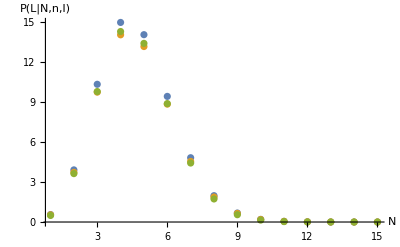

```mathematica
Block[{L=0.07,evidence,m=5,a=1/2,tmpInt,tmpLaplace,tmpDelta,N1=1,N2=15,α1=0.5,α2=3,β1=1,β2=300},
evidence=NIntegrate[Exp[logpost[α,β,samples]],{α,α1,α2},{β,β1,β2},PrecisionGoal->4];
Print[evidence];
tmpInt=ParallelTable[{Nl,NIntegrate[Exp[logmean[α,β,samples,L,Nl]],{α,α1,α2},{β,β1,β2}]/evidence},{Nl,N1,N2}];
(*Print[tmpInt];*)
Print[√((2 Pi)^2/detG)Exp[solg[[1]]]];
tmpLaplace=ParallelTable[{Nl,pL[L,Nl,solg[[1]],detG]},{Nl,N1,N2}];
tmpDelta=ParallelTable[{Nl,PDF[GammaDistribution[Nl α,1/β]/.pars,L]},{Nl,N1,N2}];
ListPlot[{tmpInt,tmpLaplace,tmpDelta},AxesLabel->{"N","P(L|N,n,l)"},PlotRange->Full]
]
```

```mathematica
solg[[2]]
```

{α→1.58983,β→90.9666}

```mathematica
hess=hessLikelihood[α,β,Length[samples]]+hessPrior[priors[α,β,jeffreys]]/.solg[[2]]
Print[Det[hess]];
Exp[-1/2 ({x,y}-{α,β}).hess.({x,y}-{α,β})]/.solg[[2]];
NIntegrate[{%,Exp[logpost[x,y,samples]],PDF[MultinormalDistribution[{α,β},Inverse[hessLikelihood[α,β,Length[samples]]+hessPrior[priors[α,β,jeffreys]]]]/.solg[[2]],{x,y}]},{x,0,2.5},{y,1,300},Method->"GaussKronrodRule"]
```

{{130.71,-1.65998},{-1.65998,2.63903}}

342.193

{0.33966,4.86583×10^202,1.}

InterpolatingFunction[{{1., 5.}}, <>]

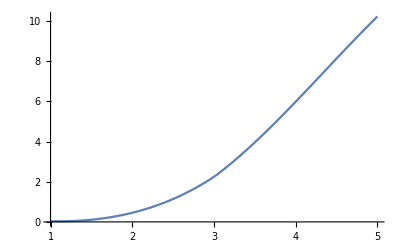

```mathematica
Block[{tmpDelta},Interpolation[ParallelTable[{Nl,PDF[GammaDistribution[Nl α,1/β]/.pars,L]},{Nl,1,5}]]
Plot[%[x],{x,1,5}]
```

Distribution of N gamma variates with α,β fixed at posterior mode

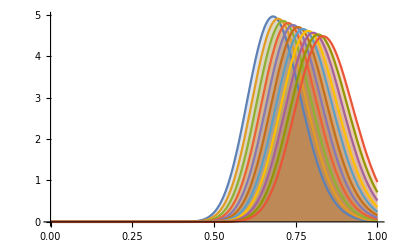

```mathematica
Plot[Evaluate[Table[PDF[GammaDistribution[n α,1/β]/.solg[[2]],x],{n,45,55}]],{x,0,1},Filling->Axis]
```

Get the posterior averages of the first and second moment

```mathematica
sol1=FindMaximum[{logpost[α,β,samples]+Log[Moment[GammaDistribution[α,1/β],1]],α>0&&β>0},{{α,1.2},{β,30}}]
laplace[sol1[[1]],detm[α,β,Length[samples],1,1]/.sol1[[2]],solg[[1]],detG]
sol2=FindMaximum[{logpost[α,β,samples]+Log[Moment[GammaDistribution[α,1/β],2]],α>0&&β>0},{{α,1.2},{β,30}}]
laplace[sol2[[1]],detm[α,β,Length[samples],2,1]/.sol2[[2]],solg[[1]],detG]
```

{157.016,{α→1.61326,β→103.893}}

0.0152638

{153.343,{α→1.58986,β→101.054}}

0.000380714

Compute mean and variance; need average of 1st moment^2

```mathematica
sol12=FindMaximum[{logpost[α,β,samples]+Log[Moment[GammaDistribution[α,1/β],1]^2],α>0&&β>0},{{α,1.2},{β,30}}]
EL[n_,a_,r1_]:=(n-a+1)r1
VL[n_,a_,r1_,r2_,r12_]:=(-1+a-n) ((1-a+n) r1^2- (r2+(2-a+n) r12))
Block[{r1,r2,r12,n=50,a=1/2},
r1=laplace[sol1[[1]],detm[α,β,Length[samples],1,1]/.sol1[[2]],solg[[1]],detG];
r2=laplace[sol2[[1]],detm[α,β,Length[samples],2,1]/.sol2[[2]],solg[[1]],detG];
r12=laplace[sol12[[1]],detm[α,β,Length[samples],1,2]/.sol12[[2]],solg[[1]],detG];
Print[{EL[n,a,r1],VL[n,a,r1,r2,r12]//Sqrt}]
]
```

{152.857,{α→1.61151,β→102.483}}

{0.770824,0.195925}

## Compare P(N|n), P(L|N,n) and their product for fixed L and variable N

```mathematica
PDF[NegativeBinomialDistribution[m+1-a,1/2],N]
```

Piecewise[{{2^(-1+a-m-N) Binomial[-a+m+N,-a+m], N≥0}, {0, True}}]

{{3/64,0.306698},{21/256,2.38641},{7/64,7.46666},{63/512,13.1261},{63/512,15.1042},{231/2048,12.5221},{99/1024,8.0188},{1287/16384,4.1868},{1001/16384,1.86141},{3003/65536,0.729972}}

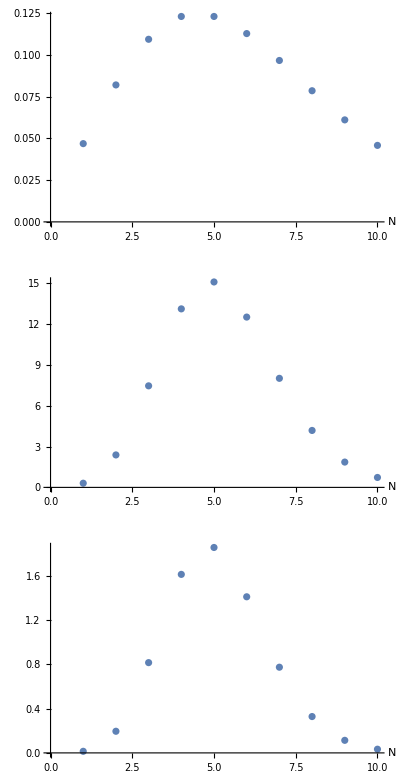

```mathematica
Block[{m=5,a=0,x=0.07,tmp},
tmp=Table[
{PDF[NegativeBinomialDistribution[m+1-a,1/2],Nl] ,pL[x,Nl,solg[[1]],detG]},
{Nl,1,10}];
Print[tmp];
GraphicsColumn[ListPlot[#,AxesLabel->{"N"}]&/@{tmp[[All,1]], tmp[[All,2]],Times@@@tmp}]
]
```

## Check if mixture distribution can be approximated by Gaussian. Certainly not for small m=5. Very slow calculation. For m=50, approximation is good. Some differences out at 1-2 σ, the approximation is low by ~20 %. Even for m=30 seems a good approx.

```mathematica
pL[x_,m_,a_]:=Sum[PDF[NegativeBinomialDistribution[m+1-a,1/2],Nl] pL[x,Nl,solg[[1]],detG],{Nl,5,55}]
(*Block[{pairs,m=30,a=1/2},
pairs=Table[{x,pL[x,m,a]},{x,0.5,3.0,0.5}];
ListPlot[pairs]
]*)
```

m=30

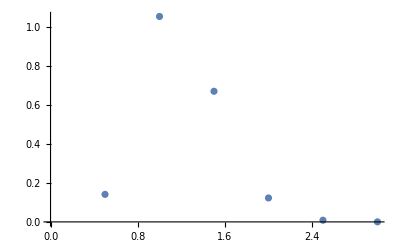

-Graphics-

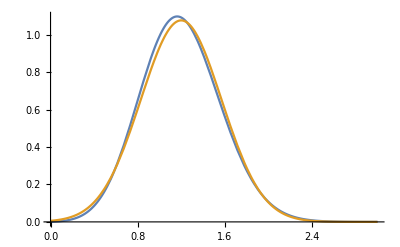

-Graphics-

m=50

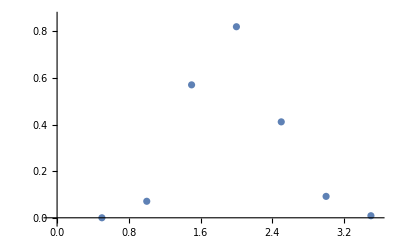

-Graphics-

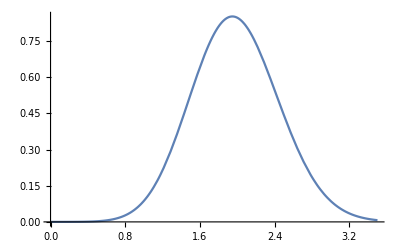

-Graphics-

0.595343

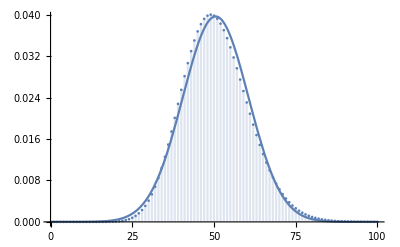

```mathematica
Block[{pairs,m=50,a=1/2},
Moment[GammaDistribution[50α,1/β],2]/.solg[[2]]//Print;
Show[{Plot[PDF[NormalDistribution[(m-a+1),√(2(m-a+1))],x],{x,0,100}],DiscretePlot[PDF[NegativeBinomialDistribution[m+1-a,1/2],Nl],{Nl,0,100}]}]
]
```

Laplace: exact solution for mode exists but is lengthy

```mathematica
Clear[var]
```

0.0251422

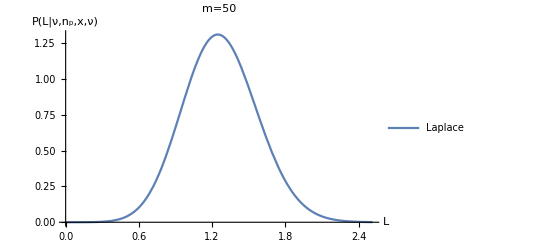

L.pdf

```mathematica
gaussApprox=PDF[NormalDistribution[(m-a+1),√(2(m-a+1))],Nl]PDF[NormalDistribution[Nl mean,√(Nl var)],x];
derivGauss=D[Log[gaussApprox],Nl]//Simplify;
solGauss=Solve[%==0,Nl][[1,1]];
hessGauss=-D[%%,Nl]//Simplify;
Block[{pairs,m=Length[samples],a=1/2,mean=Mean[samples],var=Variance[samples],
meanL=1.9847704310783707, varL=0.4812766256318326},
Print[mean];
Plot[{Re[√((2 Pi)/hessGauss)gaussApprox/.solGauss](*,PDF[NormalDistribution[meanL,varL],x]*)},{x,0 mean, 2 m mean},AxesLabel->{"L","P(L|ν,n_p,x,ν)"},PlotLabel->"m="<>ToString[m],PlotLegends->{"Laplace","Gauss"}]
(*Plot[gaussApprox,{Nl,1,100}]*)
]
Export["L.pdf",%]
```

## Compare discrete sum for scaled and unscaled inputs

```mathematica
P[L_,n_,mean_, var_]:=Module[{},Sum[PDF[NormalDistribution[Ni mean, √(Ni var)],L] PDF[NormalDistribution[n,√(2 n+1)],Ni],{Ni,1,3 n}]]
```

Result is a mixture distribution with weight given by Poisson posterior predictive. As many components/modes as there are summands. That’s a nasty function.

0.0234534

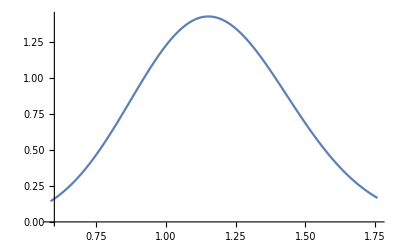

```mathematica
Block[{m=50, offset=14021,lmax,
scaledSamples,scaledMean, scaledVar,
samples,mean,var},
samples=sortedData[[offset;;offset+m-1,2]];
mean=Mean[samples];
var=Variance[samples];
scaledSamples=samples / (-Max[sortedData[[All,2]]](1+10^-6));
scaledSamples+=1;
scaledMean=Mean[scaledSamples];
scaledVar=Variance[scaledSamples];
Print[scaledMean];
(*PL=ParallelTable[{L,P[L,m,mean,var]},{L,0.5 m mean,1.5 m mean ,0.1 mean}];
ListPlot[PL]
*)
GraphicsRow[
{Plot[P[L,m,mean,var],{L,0.5 m mean,1.5 m mean }, MaxRecursion->0,PlotPoints->500],
Plot[P[L,m,scaledMean,scaledVar],{L,0.5 m scaledMean,1.5 m scaledMean }, MaxRecursion->0,PlotPoints->500]}
]
]
```

hedgehog.pdf

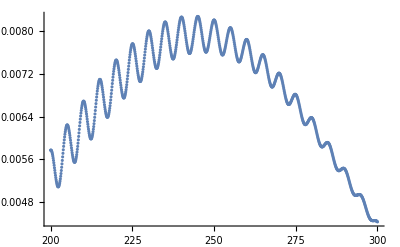

```mathematica
Export["hedgehog.pdf",%]
```

## Gaussian approximation for large n,m. ∑_N → ∫ via Laplace.

No exact solution if derivatives of Binomial coefficient appear, even with Stirling’s approximation. So approximate Negative Binomial by Gaussian. Fixing mode instead of mean for better agreement around the mode where the contribution to the integral is largest seems to give a poor fit on average, so let’s stick with mean.

```mathematica
Block[{(*μ=Mean[samples],σSq=Variance[samples],*)f,μ,σSq,sol,grad},
(*f=Assuming[Nl≥ 0&&n≥0&&a≥0&&a≤1&&σSq>0,Log[Gamma[Nl+n-a+1]]-Log[Gamma[Nl+1]]-Log[Gamma[n-a+1]]-(N+n-a+1)Log[2]+Log[PDF[NormalDistribution[Nl μ, √(Nl σSq)],L]]/.{Log[Gamma[x_]]->x Log[x]-x+1/2 Log[(2 Pi)/x]}//Simplify];*)
(*f=Log[2^(-1+a-m-Nl) Binomial[-a+m+Nl,-a+m]PDF[NormalDistribution[Nl μ, √(Nl σSq)],L]]//Simplify;*)
f=PDF[NormalDistribution[r,√(2r)],Nl]PDF[NormalDistribution[Nl μ, √(Nl σSq)],L];
Print[TraditionalForm[f]];
grad=D[Log[f],Nl]//Simplify;
Print["Gradient:"];
Print[TraditionalForm[grad]];

sol=Solve[grad==0,Nl][[1,1]];
(*Simplify[sol[[2]]];*)
Print["Hessian: "];
Print[TraditionalForm[-D[grad,Nl]//Simplify]];
]
```

(ⅇ^(-(L-μ Nl)^2/(2 Nl σSq)-(Nl-r)^2/(4 r)))/(2 √2 π √r √(Nl σSq))

Gradient:

(L^2 r-Nl (Nl^2 σSq+Nl r (μ^2-σSq)+r σSq))/(2 Nl^2 r σSq)

Hessian:

1/2 ((2 L^2)/(Nl^3 σSq)-1/Nl^2+1/r)

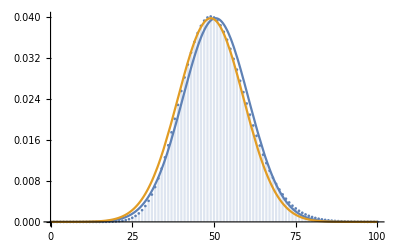

```mathematica
Block[{m=50,a=1/2,r},
r=m-a+1;Show[DiscretePlot[PDF[NegativeBinomialDistribution[r,1/2],Nl],{Nl,0,100}],Plot[{PDF[NormalDistribution[r,√(2r)],Nl],PDF[NormalDistribution[Floor[r-1],√(2r)],Nl]},{Nl,0,100}]]
]
```

Finding the mode boils down to a finding the root of a cubic polynomial. There is exactly one real solution.

```mathematica
L^2 (a-m-1)+Nl (Nl (μ^2 (-a+m+1)+σSq (a-m))+σSq (-a+m+1)+Nl^2 σSq)/.{(m-a+1)->r,a-m-1->-r,a-m->-r+1}
Expand[%]
Solve[%==0,Nl][[1,1]]
```

-L^2 r+Nl (Nl^2 σSq+r σSq+Nl (r μ^2+(1-r) σSq))

-L^2 r+Nl^2 r μ^2+Nl^2 σSq+Nl^3 σSq+Nl r σSq-Nl^2 r σSq

Nl→-(r μ^2+σSq-r σSq)/(3 σSq)-(2^(1/3) (3 r σSq^2-(r μ^2+σSq-r σSq)^2))/(3 σSq (-2 r^3 μ^6-6 r^2 μ^4 σSq+6 r^3 μ^4 σSq+27 L^2 r σSq^2-6 r μ^2 σSq^2+21 r^2 μ^2 σSq^2-6 r^3 μ^2 σSq^2-2 σSq^3+15 r σSq^3-15 r^2 σSq^3+2 r^3 σSq^3+√((-2 r^3 μ^6-6 r^2 μ^4 σSq+6 r^3 μ^4 σSq+27 L^2 r σSq^2-6 r μ^2 σSq^2+21 r^2 μ^2 σSq^2-6 r^3 μ^2 σSq^2-2 σSq^3+15 r σSq^3-15 r^2 σSq^3+2 r^3 σSq^3)^2+4 (3 r σSq^2-(r μ^2+σSq-r σSq)^2)^3))^(1/3))+1/(3 2^(1/3) σSq)(-2 r^3 μ^6-6 r^2 μ^4 σSq+6 r^3 μ^4 σSq+27 L^2 r σSq^2-6 r μ^2 σSq^2+21 r^2 μ^2 σSq^2-6 r^3 μ^2 σSq^2-2 σSq^3+15 r σSq^3-15 r^2 σSq^3+2 r^3 σSq^3+√((-2 r^3 μ^6-6 r^2 μ^4 σSq+6 r^3 μ^4 σSq+27 L^2 r σSq^2-6 r μ^2 σSq^2+21 r^2 μ^2 σSq^2-6 r^3 μ^2 σSq^2-2 σSq^3+15 r σSq^3-15 r^2 σSq^3+2 r^3 σSq^3)^2+4 (3 r σSq^2-(r μ^2+σSq-r σSq)^2)^3))^(1/3)

```mathematica
Solve[a3 n^3+a2 n^2 + a1 n + a0==0,n][[1,1]]
```

n→-a2/(3 a3)-(2^(1/3) (-a2^2+3 a1 a3))/(3 a3 (-2 a2^3+9 a1 a2 a3-27 a0 a3^2+√(4 (-a2^2+3 a1 a3)^3+(-2 a2^3+9 a1 a2 a3-27 a0 a3^2)^2))^(1/3))+((-2 a2^3+9 a1 a2 a3-27 a0 a3^2+√(4 (-a2^2+3 a1 a3)^3+(-2 a2^3+9 a1 a2 a3-27 a0 a3^2)^2))^(1/3))/(3 2^(1/3) a3)

## Prior: define shape parameter α as function of frequency.

```mathematica
Minimize[{a0+a1 x+a2 x^2,x>0&&x≤1&&{x,a0,a1,a2,a3}∈Reals},x]
```

{Piecewise[{{a0, (a2==0&&a1==0)||(a2==0&&a1>0)||(a2>0&&a1≥0)||(a2<0&&a1>-a2)}, {a0+a1, a2==0&&a1<0}, {a0+a1+a2, (a2>0&&a1≤-2 a2)||(a2<0&&a1≤-a2)}, {(-a1^2+4 a0 a2)/(4 a2), True}}],{x→Piecewise[{{1/2, a2==0&&a1==0}, {1, (a2==0&&a1<0)||(a2>0&&a1≤-2 a2)||(a2<0&&a1≤-a2)}, {-a1/(2 a2), a2>0&&-2 a2<a1<0}, {Indeterminate, True}}]}}

0.1+2.3 x

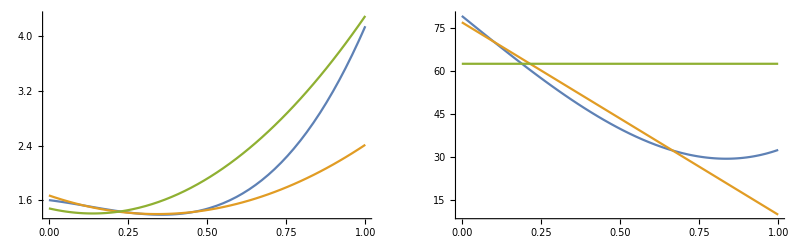

```mathematica
f[x_,an_]:=Total[Table[an[[i]] x^(i-1),{i,Length[an]}]];
f[x,{0.1,2.3}]
GraphicsRow[{Plot[Evaluate[a0+a1 x+a2 x^2+a3 x^3/.{(*{a0->1.61,a1->-9.21,a2->4.58,a3->-6.72,a4->4.51},
{a0->1.69,a1->-1.85,a2->4.79,a3->-11.1,a4->15.0},*){a0->1.6009,a1->-0.572,a2->-1.85,a3->4.97,a4->0},{a0->1.6699,a1->-1.6,a2->2.342,a3->0,a4->0},
{a0->1.48,a1->-1.08,a2->3.9,a3->0,a4->0}}],{x,0,1}],
Plot[Evaluate[b0+b1 x+b2 x^2+b3 x^3/.{{b0->79.3,b1->-89.7,b2->0,b3->42.8},{b0->77.08,b1->-67.36,b2->0,b3->0},
{b0->62.55,b1->0,b2->0,b3->0}}],{x,0,1}]}
]
```

## Hessian for Gamma linear model

```mathematica
rules={(b0+b1 ν)-> β[ν],(a0+a1 ν + a2 ν^2+a3 ν^3)->α[ν],-a0-a1 ν - a2 ν^2-a3 ν^3->-α[ν],a0+ν (a1+ν (a2+a3 ν))->α[ν]}
```

{b0+b1 ν→β[ν],a0+a1 ν+a2 ν^2+a3 ν^3→α[ν],-a0-a1 ν-a2 ν^2-a3 ν^3→-α[ν],a0+ν (a1+ν (a2+a3 ν))→α[ν]}

P(x|Nα,β)

```mathematica
pNa=PDF[GammaDistribution[Nb (a0+a1 ν + a2 ν^2+a3 ν^3), 1/(b0+b1 ν)],x][[1,1,1]]//Log
{D[pNa,a1],D[pNa,b1],D[pNa,Nb]};
%/.rules//Simplify//TraditionalForm
(-{D[pNa,a1,a1],D[pNa,a1,b1],D[pNa,a1,Nb],D[pNa,b1,b1],D[pNa,b1,Nb],D[pNa,Nb,Nb]})//Simplify;
%/.rules//Simplify//TraditionalForm
```

Log[(ⅇ^(-x (b0+b1 ν)) x^(-1+Nb (a0+a1 ν+a2 ν^2+a3 ν^3)) (1/(b0+b1 ν))^(-Nb (a0+a1 ν+a2 ν^2+a3 ν^3)))/Gamma[Nb (a0+a1 ν+a2 ν^2+a3 ν^3)]]

{ν Nb (-log(1/(β(ν)))-0Nb α(ν)+log(x)),(ν Nb α(ν))/(β(ν))-ν x,α(ν) (-log(1/(β(ν)))-0Nb α(ν)+log(x))}

{ν^2 Nb^2 1Nb α(ν),-(ν^2 Nb)/(β(ν)),ν (log(1/(β(ν)))+0Nb α(ν)+Nb α(ν) 1Nb α(ν)-log(x)),(ν^2 Nb α(ν))/(β(ν))^2,-(ν α(ν))/(β(ν)),(α(ν))^2 1Nb α(ν)}

P(N|n)

0-a+n+Nb+1-0Nb+1-log(2)

1Nb+1-1-a+n+Nb+1

{-117.197,0.331242}

{-5.00647,{Nb→1775.}}

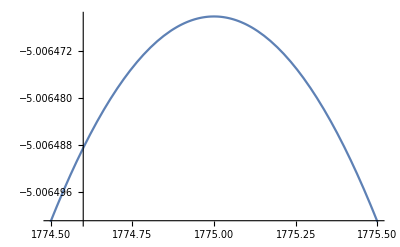

59.7578

```mathematica
nb=Log[Gamma[Nb+n-a+1]]-Log[Gamma[Nb+1]]-Log[Gamma[n-a+1]]-(Nb+n-a+1)Log[2];
D[nb,Nb]//TraditionalForm
-D[nb,{Nb,2}]//TraditionalForm
{nb,D[nb,Nb]}/.{n->1785,a->1/2.,Nb->999}
FindMaximum[nb/.{n->1776,a->1/2.},{Nb,1000}]
Plot[nb/.{n->1776,a->1/2.},{Nb, 1774.5, 1775.5}]
√(2 1785.+1)
```

P(x|α,β)

```mathematica
pa=PDF[GammaDistribution[ (a0+a1 ν + a2 ν^2+a3 ν^3), 1/(b0+b1 ν)],x][[1,1,1]]//Log
{D[pa,a1],D[pa,b1]}/.rules//Simplify
%/.{α[ν]->1.60079,β[ν]-> 75.7531,ν-> 0.019,x-> 0.05353}(*{α[ν]->1.60081,β[ν]-> 75.80156,ν-> 0.014794,x-> 0.02813741365235245}*)
(-{D[pa,a1,a1],D[pa,a1,b1],D[pa,b1,b1]})//Simplify;
%/.rules//Simplify//TraditionalForm
```

Log[(ⅇ^(-x (b0+b1 ν)) x^(-1+a0+a1 ν+a2 ν^2+a3 ν^3) (1/(b0+b1 ν))^(-a0-a1 ν-a2 ν^2-a3 ν^3))/Gamma[a0+a1 ν+a2 ν^2+a3 ν^3]]

{ν (Log[x]-Log[1/β[ν]]-PolyGamma[0,α[ν]]),-x ν+(ν α[ν])/β[ν]}

{0.0241916,-0.000615568}

{ν^2 1α(ν),-ν^2/(β(ν)),(ν^2 α(ν))/(β(ν))^2}